```mathematica
(*Riemman in optical metric*)
```

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)
```

```mathematica
DefManifold[M2,2,IndexRange[a,n]]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

```mathematica
DefChart[esfOp,M2,{1,2},{r[],Φ[]},ChartColor->Brown]
```

```mathematica
(*metric field*)
DefScalarFunction[hh,PrintAs->"h"]
DefScalarFunction[ff,PrintAs->"f"]
```

```mathematica
$Assumptions={r[]>0,Φ[]>0,Φ[]<2π};
MatrixForm[metricarray={{1/(ff[r[]]hh[r[]]),0},{0,r[]^2/hh[r[]]}}]
```

(1/(f[r] h[r]) | 0
0 | r^2/h[r])

```mathematica
metric2=CTensor[metricarray,{-esfOp,-esfOp}];
Invmetric2 =Inv[metric2];
```

```mathematica
(*CD=LC[metric]*)
cd=CovDOfMetric[metric2];
pd=PDOfBasis[esfOp];
```

```mathematica
Riemanncd=Riemann[cd];
```

```mathematica
rules={metric[a_?DownIndexQ,b_?DownIndexQ]:>metric2[a,b],
metric[a_?UpIndexQ,b_?UpIndexQ]:>Invmetric2[a,b],Det[g[]]->Det[metricarray],RiemannCD[a_?DownIndexQ,b_?DownIndexQ,c_?DownIndexQ,d_?DownIndexQ]:>Riemanncd[a,b,c,d]};
```

```mathematica
(* Vias 1*)
temp=RiemannCD[-a,-b,-c,-d]/Det[g[]];
temp2=temp//.rules;
Result=Head[temp2];
(*Result[[1, 3, 1, 3]]*)
```

```mathematica
(*total curvature K=R_{rϕrϕ}/dg*)
```

```mathematica
Kfunv0=-1/(√(metric2[{1,-esfOp},{1,-esfOp}]*metric2[{2,-esfOp},{2,-esfOp}]))((D[(1/(√metric2[{1,-esfOp},{1,-esfOp}])D[√metric2[{2,-esfOp},{2,-esfOp}],r[]]),r[]]+D[(1/(√metric2[{2,-esfOp},{2,-esfOp}])D[√metric2[{1,-esfOp},{1,-esfOp}],Φ[]]),Φ[]]))/.{r[]->r,Φ[]->Φ}//PowerExpand//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
Kfunv1 = (Riemann[cd][{1,-esfOp},{2,-esfOp},{1,-esfOp},{2,-esfOp}])/Det[g[]]/.rules/.{r[]->r,Φ[]->Φ}//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
Kfunv2=(RicciScalar[cd]/2/.rules)[[1]]/.{r[]->r,Φ[]->Φ}//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
Christoffel[cd,esfOp]
```

xAct`xTensor`Private`TensorPlus[Christoffel[PDesfOp,esfOp],CTensor[{{{-f'[r]/(2 f[r])-h'[r]/(2 h[r]),0},{0,(f[r] r (-2 h[r]+r h'[r]))/(2 h[r])}},{{0,1/r-h'[r]/(2 h[r])},{1/r-h'[r]/(2 h[r]),0}}},{esfOp,-esfOp,-esfOp},0]]

```mathematica
term1={{{-f'[r]/(2 f[r])-h'[r]/(2 h[r]),0},{0,(f[r] r (-2 h[r]+r h'[r]))/(2 h[r])}},{{0,1/r-h'[r]/(2 h[r])},{1/r-h'[r]/(2 h[r]),0}}}[[2,1,1]];
term={{{-f'[r]/(2 f[r])-h'[r]/(2 h[r]),0},{0,(f[r] r (-2 h[r]+r h'[r]))/(2 h[r])}},{{0,1/r-h'[r]/(2 h[r])},{1/r-h'[r]/(2 h[r]),0}}}[[2,1,2]];
```

```mathematica
Kfunv3=1/(√Det[g[]])(D[(√Det[g[]])/metric2[{1,-esfOp},{1,-esfOp}] term1/.rules,Φ[]]-D[(√Det[g[]])/metric2[{1,-esfOp},{1,-esfOp}] term/.rules,r[]])/.rules/.{r[]->r,Φ[]->Φ}//Factor
```

(-2 h[r]^2 f'[r]+2 f[r] h[r] h'[r]+r h[r] f'[r] h'[r]-2 r f[r] h'[r]^2+2 r f[r] h[r] h''[r])/(4 r h[r])

```mathematica
(*check*)
```

```mathematica
Kfunv3-Kfunv0//Simplify
```

0

```mathematica
(*Sch*)
```

```mathematica
Sch={hh->Function[r, ff[r]],ff->Function[r,1-2G M/r]}; (*ff->Function[r,1-2G M/(cc^2r)]}*)
Kott={hh->Function[r, ff[r]],ff->Function[r,1-2G M/r-Λ r^2/3]}; 
Horndk={hh->Function[r,1-2G M/r],ff->Function[r,(1-2G M/r)(1-r^2Λ)]};
```

```mathematica
KSch=Kfunv3//.Sch//Simplify//Expand//Simplify
KKot=Collect[Kfunv3//.Kott//Simplify//Expand,Λ, Simplify]
KHornd=Collect[Kfunv3//.Horndk//Simplify//Expand,Λ, Expand]
```

(G M (3 G M-2 r))/r^4

(G M (3 G M-2 r))/r^4+(-1/3+(2 G M)/r) Λ

(3 G^2 M^2)/r^4-(2 G M)/r^3+(1+(3 G^2 M^2)/r^2-(3 G M)/r) Λ

```mathematica
(*Optical metric*)
```

```mathematica
OptMeKot=metric[-a, -b]/.rules/.{r[]->r,Φ[]->Φ}//.Kott//PowerExpand//FullSimplify;
OptMeHornd=metric[-a, -b]/.rules/.{r[]->r,Φ[]->Φ}//.Horndk//PowerExpand//FullSimplify;
```

```mathematica
Head[OptMeKot]/.r->b/u/.G->rs/(2M)/.Λ->rs λ/b^3/.rs->Rs*b//FullSimplify
Head[OptMeHornd]/.r->b/u/.G->rs/(2M)/.Λ->rs λ/b^3/.rs->Rs*b//FullSimplify
```

CTensor[{{(9 u^4)/((3 u^2 (-1+Rs u)+Rs λ)^2),0},{0,-(3 b^2)/(3 u^2 (-1+Rs u)+Rs λ)}},{-esfOp,-esfOp},0]

CTensor[{{1/((-1+Rs u)^2 (1-(Rs λ)/u^2)),0},{0,b^2/(u^2-Rs u^3)}},{-esfOp,-esfOp},0]

```mathematica
OptMeHornd
```

1/((1-(2 G M)/r)^2 (1-r^2 Λ)) | 0
0 | r^3/(-2 G M+r) |   |  
a | b

```mathematica
(*Horndeski*)
```

```mathematica
√Det[g[]]/.rules/.{r[]->r,Φ[]->Φ}//.Horndk//PowerExpand//Simplify
```

r/((1-(2 G M)/r)^(3/2) √(1-r^2 Λ))

```mathematica
Solve[D[r[ϕ],ϕ]+ff[r]r^2==r^4 ff[r]/(b^2 hh[r])//.Horndk,D[r[ϕ],ϕ]]//Expand
```

{{r'[ϕ]→2 G M r-r^2+r^4/b^2-2 G M r^3 Λ+r^4 Λ-(r^6 Λ)/b^2}}

```mathematica
(*angle*)
```

```mathematica
tan=Sqrt[ff[r]]r D[ϕ[r],r]//.Horndk//PowerExpand//Simplify
```

√(1-(2 G M)/r) r √(1-r^2 Λ) ϕ'[r]

```mathematica
(*geodesicas*)
```

```mathematica
Eq1= D[u[ϕ],ϕ]^2+u[ϕ]^2(1-u[ϕ]);
DSolve[Eq1==0, u[ϕ],ϕ]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{u[ϕ]→1+Tan[1/2 (-ϕ+C[1])]^2},{u[ϕ]→1+Tan[(ϕ+C[1])/2]^2}}

```mathematica
DSolve[{Eq1==c1+c2}, u[ϕ],ϕ]
```

```mathematica
$Assumptions=M>=0&&G>=0
```

M≥0&&G≥0

```mathematica
(*Analisis de la serie*)
```

```mathematica
Quit[]
```

```mathematica
√(1-(2 G M)/r[ϕ])  √(1-r[ϕ]^2 Λ) r[ϕ]/r'[ϕ]/.r->Function[ϕ,b/u[ϕ]]/.G->rs/(2M)/.Λ->rs λ/b^3/.rs->Rs*b//Simplify
```

-(√(1-(Rs λ)/u[ϕ]^2) u[ϕ] √(1-Rs u[ϕ]))/u'[ϕ]

```mathematica
eq=Last@Solve[((r'[ϕ])^2==2 G M r[ϕ]-r[ϕ]^2+r[ϕ]^4/b^2-2 G M r[ϕ]^3 Λ+r[ϕ]^4 Λ-(r[ϕ]^6 Λ)/b^2/.r->Function[ϕ,b/u[ϕ]]/.G->rs/(2M)/.Λ->rs λ/b^3/.rs->Rs*b/.u'[ϕ]^2->u2//Simplify//Expand),u2]/.Rule->Equal/.u2->u'[ϕ]^2//Expand
```

{u'[ϕ]^2==1+Rs λ-(Rs λ)/u[ϕ]^2-Rs^2 λ u[ϕ]-u[ϕ]^2+Rs u[ϕ]^3}

```mathematica
(*Λ̄=Λ̂/(Rs b^2)*)
```

```mathematica
(*multiplico por u[ϕ]^2 *)
eq1=(eq[[1,1]]-eq[[1,2]])*u[ϕ]^2//Expand
```

Rs λ-u[ϕ]^2-Rs λ u[ϕ]^2+Rs^2 λ u[ϕ]^3+u[ϕ]^4-Rs u[ϕ]^5+u[ϕ]^2 u'[ϕ]^2

```mathematica
(* ϵ -> rs/b=Rs *)
```

```mathematica
rU=u->Function[ϕ, (u0[ϕ]+ϵ u1[ϕ]+ϵ^2 u2[ϕ]+ϵ^3 u3[ϕ]+ϵ^4 u4[ϕ])];
(*rS=Rs->0+ϵ Rs+ϵ^2 Rs+ϵ^3 Rs;*)
(*rS=Rs->0+ϵ Rs+ϵ^2 Rs+ϵ^3 Rs;*)
(*ΛS=Λ̄->0+ϵ Λ̄*)
```

```mathematica
test=Collect[eq1/.rU/.ϵ->Rs,Rs ,Simplify];(*/.ΛS/.rS,*)
```

```mathematica
test0=Coefficient[test,Rs,0]
test1=Coefficient[test,Rs,1]
test2=Coefficient[test,Rs,2]
test3=Coefficient[test,Rs,3]
test4=Coefficient[test,Rs,4]
```

u0[ϕ]^2 (-1+u0[ϕ]^2+u0'[ϕ]^2)

λ-u0[ϕ]^5+4 u0[ϕ]^3 u1[ϕ]+2 u0[ϕ] u1[ϕ] (-1+u0'[ϕ]^2)-u0[ϕ]^2 (λ-2 u0'[ϕ] u1'[ϕ])

-5 u0[ϕ]^4 u1[ϕ]+u0[ϕ]^3 (λ+4 u2[ϕ])+u1[ϕ]^2 (-1+u0'[ϕ]^2)+2 u0[ϕ] u2[ϕ] (-1+u0'[ϕ]^2)-2 u0[ϕ] u1[ϕ] (λ-2 u0'[ϕ] u1'[ϕ])+u0[ϕ]^2 (6 u1[ϕ]^2+u1'[ϕ]^2+2 u0'[ϕ] u2'[ϕ])

-5 u0[ϕ]^4 u2[ϕ]+u0[ϕ]^3 (-10 u1[ϕ]^2+4 u3[ϕ])+u1[ϕ] (2 u2[ϕ] (-1+u0'[ϕ]^2)-u1[ϕ] (λ-2 u0'[ϕ] u1'[ϕ]))+2 u0[ϕ] (2 u1[ϕ]^3+u3[ϕ] (-1+u0'[ϕ]^2)-u2[ϕ] (λ-2 u0'[ϕ] u1'[ϕ])+u1[ϕ] (u1'[ϕ]^2+2 u0'[ϕ] u2'[ϕ]))+u0[ϕ]^2 (3 u1[ϕ] (λ+4 u2[ϕ])+2 (u1'[ϕ] u2'[ϕ]+u0'[ϕ] u3'[ϕ]))

u1[ϕ]^4-5 u0[ϕ]^4 u3[ϕ]+4 u0[ϕ]^3 (-5 u1[ϕ] u2[ϕ]+u4[ϕ])+u2[ϕ]^2 (-1+u0'[ϕ]^2)-2 u1[ϕ] (λ u2[ϕ]+u3[ϕ]-u3[ϕ] u0'[ϕ]^2-2 u2[ϕ] u0'[ϕ] u1'[ϕ])+u1[ϕ]^2 (u1'[ϕ]^2+2 u0'[ϕ] u2'[ϕ])+u0[ϕ] (3 u1[ϕ]^2 (λ+4 u2[ϕ])-2 λ u3[ϕ]-2 u4[ϕ]+2 u4[ϕ] u0'[ϕ]^2+4 u3[ϕ] u0'[ϕ] u1'[ϕ]+2 u2[ϕ] u1'[ϕ]^2+4 u2[ϕ] u0'[ϕ] u2'[ϕ]+4 u1[ϕ] (u1'[ϕ] u2'[ϕ]+u0'[ϕ] u3'[ϕ]))+u0[ϕ]^2 (-10 u1[ϕ]^3+3 λ u2[ϕ]+6 u2[ϕ]^2+12 u1[ϕ] u3[ϕ]+u2'[ϕ]^2+2 u1'[ϕ] u3'[ϕ]+2 u0'[ϕ] u4'[ϕ])

```mathematica
Sl0=Solve[test0==0,u0'[ϕ]]//Expand
Sl1=Last@Solve[test1==0,u1'[ϕ]]//Expand//Simplify
Sl2=Last@Solve[test2==0,u2'[ϕ]]//Expand//Simplify
Sl3=Last@Solve[test3==0,u3'[ϕ]]//Expand//Simplify
Sl4=Last@Solve[test4==0,u4'[ϕ]]//Expand//Simplify
```

{{u0'[ϕ]→-√(1-u0[ϕ]^2)},{u0'[ϕ]→√(1-u0[ϕ]^2)}}

{u1'[ϕ]→(-λ+λ u0[ϕ]^2+u0[ϕ]^5-4 u0[ϕ]^3 u1[ϕ]-2 u0[ϕ] u1[ϕ] (-1+u0'[ϕ]^2))/(2 u0[ϕ]^2 u0'[ϕ])}

{u2'[ϕ]→-(-5 u0[ϕ]^4 u1[ϕ]+u0[ϕ]^3 (λ+4 u2[ϕ])+u1[ϕ]^2 (-1+u0'[ϕ]^2)+2 u0[ϕ] u2[ϕ] (-1+u0'[ϕ]^2)-2 u0[ϕ] u1[ϕ] (λ-2 u0'[ϕ] u1'[ϕ])+u0[ϕ]^2 (6 u1[ϕ]^2+u1'[ϕ]^2))/(2 u0[ϕ]^2 u0'[ϕ])}

{u3'[ϕ]→1/(2 u0[ϕ]^2 u0'[ϕ])(5 u0[ϕ]^4 u2[ϕ]+2 u0[ϕ]^3 (5 u1[ϕ]^2-2 u3[ϕ])+u1[ϕ] (-2 u2[ϕ] (-1+u0'[ϕ]^2)+u1[ϕ] (λ-2 u0'[ϕ] u1'[ϕ]))-u0[ϕ]^2 (3 u1[ϕ] (λ+4 u2[ϕ])+2 u1'[ϕ] u2'[ϕ])-2 u0[ϕ] (2 u1[ϕ]^3+u3[ϕ] (-1+u0'[ϕ]^2)-u2[ϕ] (λ-2 u0'[ϕ] u1'[ϕ])+u1[ϕ] (u1'[ϕ]^2+2 u0'[ϕ] u2'[ϕ])))}

{u4'[ϕ]→-1/(2 u0[ϕ]^2 u0'[ϕ])(u1[ϕ]^4-5 u0[ϕ]^4 u3[ϕ]+4 u0[ϕ]^3 (-5 u1[ϕ] u2[ϕ]+u4[ϕ])+u2[ϕ]^2 (-1+u0'[ϕ]^2)-2 u1[ϕ] (λ u2[ϕ]+u3[ϕ]-u3[ϕ] u0'[ϕ]^2-2 u2[ϕ] u0'[ϕ] u1'[ϕ])+u1[ϕ]^2 (u1'[ϕ]^2+2 u0'[ϕ] u2'[ϕ])+u0[ϕ]^2 (-10 u1[ϕ]^3+3 λ u2[ϕ]+6 u2[ϕ]^2+12 u1[ϕ] u3[ϕ]+u2'[ϕ]^2+2 u1'[ϕ] u3'[ϕ])+u0[ϕ] (3 u1[ϕ]^2 (λ+4 u2[ϕ])-2 λ u3[ϕ]-2 u4[ϕ]+2 u4[ϕ] u0'[ϕ]^2+4 u3[ϕ] u0'[ϕ] u1'[ϕ]+2 u2[ϕ] u1'[ϕ]^2+4 u2[ϕ] u0'[ϕ] u2'[ϕ]+4 u1[ϕ] (u1'[ϕ] u2'[ϕ]+u0'[ϕ] u3'[ϕ])))}

```mathematica
(*orden cero*)
```

```mathematica
$Assumptions=ϕ>0&&ϕ<π;
```

```mathematica
s0=Last@DSolve[Sl0[[1]]/.Rule->Equal,u0[ϕ],ϕ](*Sl0[[1]]*)
c0=Last@Solve[D[s0,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1],Reals]
```

{u0[ϕ]→-Sin[ϕ-C[1]]}

{C[1]→ConditionalExpression[-π+δ-2 π C[2], C[2]∈ℤ]}

```mathematica
soF=u0->Function[ϕ,Evaluate[(s0/.c0/.C[2]->0)[[1,2]]]]
```

u0→Function[ϕ,-Sin[δ-ϕ]]

```mathematica
Sl1Eq=Sl1/.soF//Simplify
```

{u1'[ϕ]→-Csc[2 δ-2 ϕ] Csc[δ-ϕ] (λ-λ Sin[δ-ϕ]^2+Sin[δ-ϕ]^5-2 Sin[δ-ϕ]^3 u1[ϕ])}

```mathematica
s1=Last@DSolve[Sl1Eq/.Rule->Equal,u1[ϕ],ϕ]//FullSimplify
c0=Last@Solve[D[s1,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1],Reals]//FullSimplify
```

{u1[ϕ]→-1/8 Csc[δ-ϕ] (2 λ+2 λ Cos[2 δ-2 ϕ]-Sin[3 δ-3 ϕ]-4 C[1] Sin[2 δ-2 ϕ]-5 Sin[δ-ϕ])}

{C[1]→0}

```mathematica
s1F=u1->Function[ϕ,Evaluate[(s1/.c0)[[1,2]]//FullSimplify]]
```

u1→Function[ϕ,-1/8 Csc[δ-ϕ] (2 λ+2 λ Cos[2 δ-2 ϕ]-Sin[3 δ-3 ϕ]-5 Sin[δ-ϕ])]

```mathematica
Sl2Eq=Sl2/.soF/.s1F//FullSimplify
```

{u2'[ϕ]→-1/1024 Csc[δ-ϕ]^4 Sec[δ-ϕ] (-3 (61+48 λ^2)+3 Cos[8 δ-8 ϕ]+24 Cos[6 δ-6 ϕ]-4 (35+12 λ^2) Cos[4 δ-4 ϕ]+8 (37-24 λ^2) Cos[2 δ-2 ϕ]+8 λ (Sin[7 δ-7 ϕ]+Sin[5 δ-5 ϕ]+116 Cos[δ-ϕ]^2 Sin[δ-ϕ])-1024 Sin[δ-ϕ]^5 u2[ϕ])}

```mathematica
Last@DSolve[Sl2Eq/.Rule->Equal,u2[ϕ],ϕ]//TrigToExp//FullSimplify
```

{u2[ϕ]→1/64 ((-60 ϕ+64 C[1]) Cos[δ-ϕ]-2 λ Cot[δ-ϕ] Csc[δ] Csc[δ-ϕ]^2 (-Cos[3 δ-4 ϕ]+Cos[5 δ-4 ϕ]+6 Cos[δ-2 ϕ]-6 Cos[3 δ-2 ϕ]+λ Sin[2 δ-3 ϕ]-3 λ Sin[2 δ-ϕ])+1/2 Sec[δ] (3 (Sin[2 δ-3 ϕ]+Sin[4 δ-3 ϕ]+Sin[2 δ-ϕ])+77 Sin[ϕ]))}

```mathematica
s2=Last@DSolve[Sl2Eq/.Rule->Equal,u2[ϕ],ϕ]//TrigToExp//FullSimplify
c0=Last@Solve[D[s2,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1]]//FullSimplify
```

{u2[ϕ]→1/64 ((-60 ϕ+64 C[1]) Cos[δ-ϕ]-2 λ Cot[δ-ϕ] Csc[δ] Csc[δ-ϕ]^2 (-Cos[3 δ-4 ϕ]+Cos[5 δ-4 ϕ]+6 Cos[δ-2 ϕ]-6 Cos[3 δ-2 ϕ]+λ Sin[2 δ-3 ϕ]-3 λ Sin[2 δ-ϕ])+1/2 Sec[δ] (3 (Sin[2 δ-3 ϕ]+Sin[4 δ-3 ϕ]+Sin[2 δ-ϕ])+77 Sin[ϕ]))}

{C[1]→1/32 (-4 λ^2 Cot[δ]+5 (3 π+6 δ-4 Tan[δ]))}

```mathematica
s2F=u2->Function[ϕ,Evaluate[(s2/.c0)[[1,2]]//FullSimplify]]
```

u2→Function[ϕ,1/512 Csc[δ-ϕ]^3 (-114+24 λ^2+3 Cos[6 δ-6 ϕ]+(-46+8 λ^2) Cos[4 δ-4 ϕ]+(157+32 λ^2) Cos[2 δ-2 ϕ]+16 (λ Sin[5 δ-5 ϕ]-5 λ Sin[3 δ-3 ϕ]-6 λ Sin[δ-ϕ]+15 (π+2 δ-2 ϕ) Cos[δ-ϕ] Sin[δ-ϕ]^3))]

```mathematica
Sl3Eq=Sl3/.soF/.s1F/.s2F//FullSimplify
```

{u3'[ϕ]→-1/16384 Csc[δ-ϕ]^6 Sec[δ-ϕ] (1236 λ+1600 λ^3+2 λ (-18 Cos[8 δ-8 ϕ]+(-459+80 λ^2) Cos[6 δ-6 ϕ]+30 (4 (-5+4 λ^2) Cos[4 δ-4 ϕ]+5 (3+8 λ^2) Cos[2 δ-2 ϕ])+9 Cos[10 (δ-ϕ)])+49 Sin[9 δ-9 ϕ]-453 Sin[7 δ-7 ϕ]+2079 Sin[5 δ-5 ϕ]-5358 Sin[3 δ-3 ϕ]+8442 Sin[δ-ϕ]+48 (-512 λ^2 Cos[δ-ϕ]^4 Sin[δ-ϕ]+5 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ]^3 (4 λ-Sin[3 δ-3 ϕ]+3 Sin[δ-ϕ]))-3 Sin[11 (δ-ϕ)]-16384 Sin[δ-ϕ]^7 u3[ϕ])}

```mathematica
s3=Last@Collect[DSolve[Sl3Eq/.Rule->Equal,u3[ϕ],ϕ]//TrigToExp//Simplify//ExpToTrig//Simplify,λ,FullSimplify]
c0=Last@Solve[D[s3,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1]]//FullSimplify
```

{u3[ϕ]→1/128 λ^3 (8 Cos[ϕ] Csc[δ]-(5+3 Cos[4 δ-4 ϕ]) Csc[δ-ϕ]^5)+3/64 λ^2 Cos[δ-ϕ] ((Cos[3 δ-3 ϕ]+7 Cos[δ-ϕ]) Csc[δ-ϕ]^4-4 Log[Cos[(δ-ϕ)/2]]+4 Log[Sin[(δ-ϕ)/2]])+1/128 (225-Cos[4 δ-4 ϕ]+96 Cos[2 δ-2 ϕ]+128 C[1] Cos[δ-ϕ]+30 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])+1/256 λ (Cos[ϕ] Csc[δ] (-65+9 Cos[2 δ]+36 ϕ Sin[2 δ])+2 ((92-30 (π+2 δ-2 ϕ) Cot[δ]) Csc[δ-ϕ]-64 Csc[δ-ϕ]^3-30 (π+2 δ-2 ϕ) Csc[δ] Csc[δ-ϕ]^2 Sin[ϕ]+9 (-Cos[3 ϕ] Sin[3 δ]+(Cos[δ]+4 ϕ Sin[δ]) Sin[ϕ]+Cos[3 δ] Sin[3 ϕ])))}

{C[1]→-1/64 λ (18 δ+3 π (3+4 ⅈ λ)+2 (-7+2 λ^2) Cot[δ])}

```mathematica
s3F=u3->Function[ϕ,Evaluate[(s3/.c0)[[1,2]]//TrigToExp//Simplify//ExpToTrig//FullSimplify]]
```

u3→Function[ϕ,1/4096 Csc[δ-ϕ]^5 (-245 λ-80 λ^3+9 λ Cos[8 δ-8 ϕ]-8 (λ+λ^3) Cos[6 δ-6 ϕ]+4 λ (59-12 λ^2) Cos[4 δ-4 ϕ]+8 λ (1-15 λ^2) Cos[2 δ-2 ϕ]-Sin[9 δ-9 ϕ]+101 Sin[7 δ-7 ϕ]-40 Sin[5 δ-5 ϕ]-1184 Sin[3 δ-3 ϕ]+3054 Sin[δ-ϕ]+12 Sin[2 δ-2 ϕ] (λ (-29 π-58 δ-12 ⅈ π λ+58 ϕ)+8 λ^2 Cos[3 δ-3 ϕ]+32 π λ Cos[2 δ-2 ϕ]+64 δ λ Cos[2 δ-2 ϕ]+16 ⅈ π λ^2 Cos[2 δ-2 ϕ]-64 λ ϕ Cos[2 δ-2 ϕ]+56 λ^2 Cos[δ-ϕ]-12 λ^2 Log[Cos[(δ-ϕ)/2]]+16 λ^2 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]+12 λ^2 Log[Sin[(δ-ϕ)/2]]-16 λ^2 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+λ Cos[4 δ-4 ϕ] (-3 π-6 δ-4 ⅈ π λ+6 ϕ-4 λ Log[Cos[(δ-ϕ)/2]]+4 λ Log[Sin[(δ-ϕ)/2]])+5 π Sin[5 δ-5 ϕ]+10 δ Sin[5 δ-5 ϕ]-10 ϕ Sin[5 δ-5 ϕ]-25 π Sin[3 δ-3 ϕ]-50 δ Sin[3 δ-3 ϕ]+50 ϕ Sin[3 δ-3 ϕ]+50 (π+2 δ-2 ϕ) Sin[δ-ϕ]))]

```mathematica
Sl4Eq=Collect[Sl4/.soF/.s1F/.s2F/.s3F//TrigToExp//Simplify//ExpToTrig//Simplify,λ,FullSimplify];
```

```mathematica
s4=Last@Collect[DSolve[Sl4Eq/.Rule->Equal,u4[ϕ],ϕ]//TrigToExp//Simplify//ExpToTrig,λ,Simplify];
c0=Last@Solve[D[s4,ϕ][[1,2]]==0/.ϕ->π/2+δ, C[1]]//ExpToTrig//FullSimplify
```

{C[1]→(-80 λ^2 (4+λ^2) Cot[δ]+3 (1085 (π+2 δ)-72 (π+2 δ) λ^2-96 ⅈ π λ^3+(-1232+75 (π+2 δ)^2) Tan[δ]))/2048}

```mathematica
s4F=u4->Function[ϕ,Evaluate[(s4/.c0)[[1,2]]//TrigToExp//Simplify//ExpToTrig//Simplify]]
```

u4→Function[ϕ,-1/524288 Csc[δ-ϕ]^7 (243964-15750 π^2-63000 π δ-63000 δ^2-25200 λ^2-5600 λ^4+63000 π ϕ+126000 δ ϕ-63000 ϕ^2-2 (225 π^2+900 π (δ-ϕ)+2 (-3439+450 δ^2+52 λ^2+40 λ^4-900 δ ϕ+450 ϕ^2)) Cos[8 δ-8 ϕ]-5376 π λ Cos[7 δ-7 ϕ]-10752 δ λ Cos[7 δ-7 ϕ]-2688 ⅈ π λ^2 Cos[7 δ-7 ϕ]+10752 λ ϕ Cos[7 δ-7 ϕ]-72843 Cos[6 δ-6 ϕ]+3600 π^2 Cos[6 δ-6 ϕ]+14400 π δ Cos[6 δ-6 ϕ]+14400 δ^2 Cos[6 δ-6 ϕ]+12504 λ^2 Cos[6 δ-6 ϕ]-1280 λ^4 Cos[6 δ-6 ϕ]-14400 π ϕ Cos[6 δ-6 ϕ]-28800 δ ϕ Cos[6 δ-6 ϕ]+14400 ϕ^2 Cos[6 δ-6 ϕ]+30720 π λ Cos[5 δ-5 ϕ]+61440 δ λ Cos[5 δ-5 ϕ]+7680 ⅈ π λ^2 Cos[5 δ-5 ϕ]-61440 λ ϕ Cos[5 δ-5 ϕ]+215363 Cos[4 δ-4 ϕ]-12600 π^2 Cos[4 δ-4 ϕ]-50400 π δ Cos[4 δ-4 ϕ]-50400 δ^2 Cos[4 δ-4 ϕ]+25408 λ^2 Cos[4 δ-4 ϕ]-4480 λ^4 Cos[4 δ-4 ϕ]+50400 π ϕ Cos[4 δ-4 ϕ]+100800 δ ϕ Cos[4 δ-4 ϕ]-50400 ϕ^2 Cos[4 δ-4 ϕ]-67584 π λ Cos[3 δ-3 ϕ]-135168 δ λ Cos[3 δ-3 ϕ]-10752 ⅈ π λ^2 Cos[3 δ-3 ϕ]+135168 λ ϕ Cos[3 δ-3 ϕ]-399166 Cos[2 δ-2 ϕ]+25200 π^2 Cos[2 δ-2 ϕ]+100800 π δ Cos[2 δ-2 ϕ]+100800 δ^2 Cos[2 δ-2 ϕ]-12432 λ^2 Cos[2 δ-2 ϕ]-8960 λ^4 Cos[2 δ-2 ϕ]-100800 π ϕ Cos[2 δ-2 ϕ]-201600 δ ϕ Cos[2 δ-2 ϕ]+100800 ϕ^2 Cos[2 δ-2 ϕ]+41472 π λ Cos[δ-ϕ]+82944 δ λ Cos[δ-ϕ]+5376 ⅈ π λ^2 Cos[δ-ϕ]-82944 λ ϕ Cos[δ-ϕ]-1079 Cos[10 (δ-ϕ)]-72 λ^2 Cos[10 (δ-ϕ)]+5 Cos[12 (δ-ϕ)]-2688 λ^2 Cos[7 δ-7 ϕ] Log[Cos[(δ-ϕ)/2]]+7680 λ^2 Cos[5 δ-5 ϕ] Log[Cos[(δ-ϕ)/2]]-10752 λ^2 Cos[3 δ-3 ϕ] Log[Cos[(δ-ϕ)/2]]+5376 λ^2 Cos[δ-ϕ] Log[Cos[(δ-ϕ)/2]]+2688 λ^2 Cos[7 δ-7 ϕ] Log[Sin[(δ-ϕ)/2]]-7680 λ^2 Cos[5 δ-5 ϕ] Log[Sin[(δ-ϕ)/2]]+10752 λ^2 Cos[3 δ-3 ϕ] Log[Sin[(δ-ϕ)/2]]-5376 λ^2 Cos[δ-ϕ] Log[Sin[(δ-ϕ)/2]]+384 λ Cos[9 δ-9 ϕ] (2 π+4 δ+ⅈ π λ-4 ϕ+λ Log[Cos[(δ-ϕ)/2]]-λ Log[Sin[(δ-ϕ)/2]])-1984 λ Sin[9 δ-9 ϕ]+8130 π Sin[8 δ-8 ϕ]+16260 δ Sin[8 δ-8 ϕ]-432 π λ^2 Sin[8 δ-8 ϕ]-864 δ λ^2 Sin[8 δ-8 ϕ]-576 ⅈ π λ^3 Sin[8 δ-8 ϕ]-16260 ϕ Sin[8 δ-8 ϕ]+864 λ^2 ϕ Sin[8 δ-8 ϕ]-576 λ^3 Log[Cos[(δ-ϕ)/2]] Sin[8 δ-8 ϕ]+576 λ^3 Log[Sin[(δ-ϕ)/2]] Sin[8 δ-8 ϕ]+13504 λ Sin[7 δ-7 ϕ]+1152 λ^3 Sin[7 δ-7 ϕ]-43110 π Sin[6 δ-6 ϕ]-86220 δ Sin[6 δ-6 ϕ]+5280 π λ^2 Sin[6 δ-6 ϕ]+10560 δ λ^2 Sin[6 δ-6 ϕ]+1920 ⅈ π λ^3 Sin[6 δ-6 ϕ]+86220 ϕ Sin[6 δ-6 ϕ]-10560 λ^2 ϕ Sin[6 δ-6 ϕ]+1920 λ^3 Log[Cos[(δ-ϕ)/2]] Sin[6 δ-6 ϕ]-1920 λ^3 Log[Sin[(δ-ϕ)/2]] Sin[6 δ-6 ϕ]-43840 λ Sin[5 δ-5 ϕ]+12928 λ^3 Sin[5 δ-5 ϕ]+96540 π Sin[4 δ-4 ϕ]+193080 δ Sin[4 δ-4 ϕ]-5280 π λ^2 Sin[4 δ-4 ϕ]-10560 δ λ^2 Sin[4 δ-4 ϕ]-1920 ⅈ π λ^3 Sin[4 δ-4 ϕ]-193080 ϕ Sin[4 δ-4 ϕ]+10560 λ^2 ϕ Sin[4 δ-4 ϕ]-1920 λ^3 Log[Cos[(δ-ϕ)/2]] Sin[4 δ-4 ϕ]+1920 λ^3 Log[Sin[(δ-ϕ)/2]] Sin[4 δ-4 ϕ]+20608 λ Sin[3 δ-3 ϕ]+25728 λ^3 Sin[3 δ-3 ϕ]-94920 π Sin[2 δ-2 ϕ]-189840 δ Sin[2 δ-2 ϕ]-3552 π λ^2 Sin[2 δ-2 ϕ]-7104 δ λ^2 Sin[2 δ-2 ϕ]+384 ⅈ π λ^3 Sin[2 δ-2 ϕ]+189840 ϕ Sin[2 δ-2 ϕ]+7104 λ^2 ϕ Sin[2 δ-2 ϕ]+384 λ^3 Log[Cos[(δ-ϕ)/2]] Sin[2 δ-2 ϕ]-384 λ^3 Log[Sin[(δ-ϕ)/2]] Sin[2 δ-2 ϕ]+80000 λ Sin[δ-ϕ]+13952 λ^3 Sin[δ-ϕ]-270 π Sin[10 (δ-ϕ)]-540 δ Sin[10 (δ-ϕ)]+540 ϕ Sin[10 (δ-ϕ)]+64 λ Sin[11 (δ-ϕ)])]

```mathematica
(*Solución FInal*)
```

```mathematica
uSerie= Collect[(u0[ϕ]+Rs u1[ϕ]+Rs^2 u2[ϕ]+Rs^3 u3[ϕ]+Rs^4 u4[ϕ])/.soF/.s1F/.s2F/.s3F/.s4F,Rs,Simplify];
```

```mathematica
eqPaper=Collect[uSerie/.λ ->Λ̄/Rs//Simplify,{Rs,λ },Simplify];
```

```mathematica
ord0=Coefficient[eqPaper,Rs,0]//Simplify
ord1=Coefficient[eqPaper,Rs,1]//Simplify
ord2=Coefficient[eqPaper,Rs,2]//Simplify
ord3=Coefficient[eqPaper,Rs,3]//Simplify
```

1/128 (-64 Cos[δ-ϕ] Cot[δ-ϕ] Λ̄+16 Cos[δ-ϕ] Cot[δ-ϕ]^3 (Λ̄)^2-8 Cos[δ-ϕ] Cot[δ-ϕ]^5 (Λ̄)^3+5 Cos[δ-ϕ] Cot[δ-ϕ]^7 (Λ̄)^4-128 Sin[δ-ϕ])

1/4 (3+Cos[2 δ-2 ϕ])+1/4 (-3+Cos[2 δ-2 ϕ]) Cot[δ-ϕ]^2 Λ̄+3/128 Cot[δ-ϕ] Csc[δ-ϕ]^3 (-3 ⅈ π+2 Cos[3 δ-3 ϕ]+4 ⅈ π Cos[2 δ-2 ϕ]+14 Cos[δ-ϕ]-3 Log[Cos[(δ-ϕ)/2]]+4 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]+3 Log[Sin[(δ-ϕ)/2]]-4 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+Cos[4 δ-4 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^2-1/4096 Csc[δ-ϕ]^7 (18 ⅈ π+18 Cos[5 δ-5 ϕ]+30 ⅈ π Cos[4 δ-4 ϕ]+202 Cos[3 δ-3 ϕ]-39 ⅈ π Cos[2 δ-2 ϕ]+420 Cos[δ-ϕ]+18 Log[Cos[(δ-ϕ)/2]]+30 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-39 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-18 Log[Sin[(δ-ϕ)/2]]-30 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+39 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+9 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^3 Sin[2 δ-2 ϕ]

1/8192(128 (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ])-Cot[δ-ϕ] Csc[δ-ϕ]^4 (Λ̄)^2 (480 ⅈ π+9 Cos[7 δ-7 ϕ]+35 Cos[5 δ-5 ϕ]+288 ⅈ π Cos[4 δ-4 ϕ]-1519 Cos[3 δ-3 ϕ]-720 ⅈ π Cos[2 δ-2 ϕ]-4669 Cos[δ-ϕ]+480 Log[Cos[(δ-ϕ)/2]]+288 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-720 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-480 Log[Sin[(δ-ϕ)/2]]-288 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+720 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+48 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])+54 π Sin[5 δ-5 ϕ]+108 δ Sin[5 δ-5 ϕ]-108 ϕ Sin[5 δ-5 ϕ]-606 π Sin[3 δ-3 ϕ]-1212 δ Sin[3 δ-3 ϕ]+1212 ϕ Sin[3 δ-3 ϕ]+108 π Sin[δ-ϕ]+216 δ Sin[δ-ϕ]-216 ϕ Sin[δ-ϕ])-16 Cot[δ-ϕ] Csc[δ-ϕ]^2 Λ̄ (9 Cos[5 δ-5 ϕ]+Cos[3 δ-3 ϕ]+246 Cos[δ-ϕ]+6 (π+2 δ-2 ϕ) (-3 Sin[3 δ-3 ϕ]+29 Sin[δ-ϕ])))

1/512 (4 (225-Cos[4 δ-4 ϕ]+96 Cos[2 δ-2 ϕ]+30 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])+Cot[δ-ϕ] Csc[δ-ϕ]^3 Λ̄ (Cos[7 δ-7 ϕ]-29 Cos[5 δ-5 ϕ]+153 Cos[3 δ-3 ϕ]-381 Cos[δ-ϕ]-12 (π+2 δ-2 ϕ) (Sin[5 δ-5 ϕ]-5 Sin[3 δ-3 ϕ]+30 Sin[δ-ϕ])))

```mathematica
Collect[ord0,Λ̄,Simplify]
Collect[ord1,Λ̄,Simplify]
Collect[ord2,Λ̄,Simplify]
```

-1/2 Cos[δ-ϕ] Cot[δ-ϕ] Λ̄+1/8 Cos[δ-ϕ] Cot[δ-ϕ]^3 (Λ̄)^2-1/16 Cos[δ-ϕ] Cot[δ-ϕ]^5 (Λ̄)^3+5/128 Cos[δ-ϕ] Cot[δ-ϕ]^7 (Λ̄)^4-Sin[δ-ϕ]

1/4 (3+Cos[2 δ-2 ϕ])+1/4 (-3+Cos[2 δ-2 ϕ]) Cot[δ-ϕ]^2 Λ̄+3/128 Cot[δ-ϕ] Csc[δ-ϕ]^3 (-3 ⅈ π+2 Cos[3 δ-3 ϕ]+4 ⅈ π Cos[2 δ-2 ϕ]+14 Cos[δ-ϕ]-3 Log[Cos[(δ-ϕ)/2]]+4 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]+3 Log[Sin[(δ-ϕ)/2]]-4 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+Cos[4 δ-4 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^2-1/4096 Csc[δ-ϕ]^7 (18 ⅈ π+18 Cos[5 δ-5 ϕ]+30 ⅈ π Cos[4 δ-4 ϕ]+202 Cos[3 δ-3 ϕ]-39 ⅈ π Cos[2 δ-2 ϕ]+420 Cos[δ-ϕ]+18 Log[Cos[(δ-ϕ)/2]]+30 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-39 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-18 Log[Sin[(δ-ϕ)/2]]-30 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+39 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+9 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^3 Sin[2 δ-2 ϕ]

1/64 (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ])-1/8192 Cot[δ-ϕ] Csc[δ-ϕ]^4 (Λ̄)^2 (480 ⅈ π+9 Cos[7 δ-7 ϕ]+35 Cos[5 δ-5 ϕ]+288 ⅈ π Cos[4 δ-4 ϕ]-1519 Cos[3 δ-3 ϕ]-720 ⅈ π Cos[2 δ-2 ϕ]-4669 Cos[δ-ϕ]+480 Log[Cos[(δ-ϕ)/2]]+288 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-720 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-480 Log[Sin[(δ-ϕ)/2]]-288 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+720 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+48 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])+54 π Sin[5 δ-5 ϕ]+108 δ Sin[5 δ-5 ϕ]-108 ϕ Sin[5 δ-5 ϕ]-606 π Sin[3 δ-3 ϕ]-1212 δ Sin[3 δ-3 ϕ]+1212 ϕ Sin[3 δ-3 ϕ]+108 π Sin[δ-ϕ]+216 δ Sin[δ-ϕ]-216 ϕ Sin[δ-ϕ])-1/512 Cot[δ-ϕ] Csc[δ-ϕ]^2 Λ̄ (9 Cos[5 δ-5 ϕ]+Cos[3 δ-3 ϕ]+246 Cos[δ-ϕ]+6 (π+2 δ-2 ϕ) (-3 Sin[3 δ-3 ϕ]+29 Sin[δ-ϕ]))

```mathematica
(*De Sitter*)
```

```mathematica
dS=eqPaper/.Rs->0//FullSimplify
```

1/128 Cos[δ-ϕ] Cot[δ-ϕ] Λ̄ (64+Cot[δ-ϕ]^2 Λ̄ (-16+Cot[δ-ϕ]^2 Λ̄ (8-5 Cot[δ-ϕ]^2 Λ̄)))+Sin[δ-ϕ]

```mathematica
dS/.δ->0
```

-1/128 Cos[ϕ] Cot[ϕ] Λ̄ (-64+Cot[ϕ]^2 Λ̄ (16+Cot[ϕ]^2 Λ̄ (-8+5 Cot[ϕ]^2 Λ̄)))+Sin[ϕ]

```mathematica
(*Sch*)
```

```mathematica
ruleSch={Λ̄->0,δ->0};
```

```mathematica
Collect[eqPaper/.ruleSch//FullSimplify,Rs,Simplify]
```

1/4 Rs (3+Cos[2 ϕ])+Sin[ϕ]+(Rs^4 (15 (π-2 ϕ) (208 Cos[ϕ]-9 Cos[3 ϕ])+(2652-225 (π-2 ϕ)^2-1039 Cos[2 ϕ]+5 Cos[4 ϕ]) Sin[ϕ]))/2048+1/128 Rs^3 (225+96 Cos[2 ϕ]-Cos[4 ϕ]-30 (π-2 ϕ) Sin[2 ϕ])+1/64 Rs^2 (30 (π-2 ϕ) Cos[ϕ]+37 Sin[ϕ]-3 Sin[3 ϕ])

```mathematica
Quit[]
```

```mathematica
(*Test*)
```

```mathematica
ϕMin=10^-4;(*10^-4*)
rSf=3 10^3; (*3 km radio de Sch del sol *)
Λf = 1.1056 10^-52;(*m^-2*)
ΛfSch =Λf*rSf;(*rs^-2*)
b =10^23;(* 1/2,1, 5, 23, 25 [rs] *)
Rsval=1./b(*Rs=rs/b*) (*100 veces el radio de Sch*)
Lval=ΛfSch*b^2 (*Λ̄ = Λ b^2 -> *)
δval=0;
```

1.×10^-23

0.0033168

```mathematica
eqPaperFull=Rs (1/4 (3+Cos[2 δ-2 ϕ])+1/4 (-3+Cos[2 δ-2 ϕ]) Cot[δ-ϕ]^2 Λ̄+3/128 Cot[δ-ϕ] Csc[δ-ϕ]^3 (-3 ⅈ π+2 Cos[3 δ-3 ϕ]+4 ⅈ π Cos[2 δ-2 ϕ]+14 Cos[δ-ϕ]-3 Log[Cos[(δ-ϕ)/2]]+4 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]+3 Log[Sin[(δ-ϕ)/2]]-4 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+Cos[4 δ-4 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^2-1/4096 Csc[δ-ϕ]^7 (18 ⅈ π+18 Cos[5 δ-5 ϕ]+30 ⅈ π Cos[4 δ-4 ϕ]+202 Cos[3 δ-3 ϕ]-39 ⅈ π Cos[2 δ-2 ϕ]+420 Cos[δ-ϕ]+18 Log[Cos[(δ-ϕ)/2]]+30 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-39 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-18 Log[Sin[(δ-ϕ)/2]]-30 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+39 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+9 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^3 Sin[2 δ-2 ϕ])+1/128 (-64 Cos[δ-ϕ] Cot[δ-ϕ] Λ̄+16 Cos[δ-ϕ] Cot[δ-ϕ]^3 (Λ̄)^2-8 Cos[δ-ϕ] Cot[δ-ϕ]^5 (Λ̄)^3+5 Cos[δ-ϕ] Cot[δ-ϕ]^7 (Λ̄)^4-128 Sin[δ-ϕ])+1/2048 Rs^4 (-135 (π+2 δ-2 ϕ) Cos[3 δ-3 ϕ]+3120 (π+2 δ-2 ϕ) Cos[δ-ϕ]+(-2652+225 π^2+900 π δ+900 δ^2-900 π ϕ-1800 δ ϕ+900 ϕ^2-5 Cos[4 δ-4 ϕ]+1039 Cos[2 δ-2 ϕ]) Sin[δ-ϕ])+1/8192 Rs^2 (128 (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ])-Cot[δ-ϕ] Csc[δ-ϕ]^4 (Λ̄)^2 (480 ⅈ π+9 Cos[7 δ-7 ϕ]+35 Cos[5 δ-5 ϕ]+288 ⅈ π Cos[4 δ-4 ϕ]-1519 Cos[3 δ-3 ϕ]-720 ⅈ π Cos[2 δ-2 ϕ]-4669 Cos[δ-ϕ]+480 Log[Cos[(δ-ϕ)/2]]+288 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-720 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-480 Log[Sin[(δ-ϕ)/2]]-288 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+720 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+48 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])+54 π Sin[5 δ-5 ϕ]+108 δ Sin[5 δ-5 ϕ]-108 ϕ Sin[5 δ-5 ϕ]-606 π Sin[3 δ-3 ϕ]-1212 δ Sin[3 δ-3 ϕ]+1212 ϕ Sin[3 δ-3 ϕ]+108 π Sin[δ-ϕ]+216 δ Sin[δ-ϕ]-216 ϕ Sin[δ-ϕ])-16 Cot[δ-ϕ] Csc[δ-ϕ]^2 Λ̄ (9 Cos[5 δ-5 ϕ]+Cos[3 δ-3 ϕ]+246 Cos[δ-ϕ]+6 (π+2 δ-2 ϕ) (-3 Sin[3 δ-3 ϕ]+29 Sin[δ-ϕ])))+1/512 Rs^3 (4 (225-Cos[4 δ-4 ϕ]+96 Cos[2 δ-2 ϕ]+30 (π+2 δ-2 ϕ) Sin[2 δ-2 ϕ])+Cot[δ-ϕ] Csc[δ-ϕ]^3 Λ̄ (Cos[7 δ-7 ϕ]-29 Cos[5 δ-5 ϕ]+153 Cos[3 δ-3 ϕ]-381 Cos[δ-ϕ]-12 (π+2 δ-2 ϕ) (Sin[5 δ-5 ϕ]-5 Sin[3 δ-3 ϕ]+30 Sin[δ-ϕ])));
```

```mathematica
serPaper=Rs (1/4 (3+Cos[2 δ-2 ϕ])+1/4 (-3+Cos[2 δ-2 ϕ]) Cot[δ-ϕ]^2 Λ̄+3/128 Cot[δ-ϕ] Csc[δ-ϕ]^3 (-3 ⅈ π+2 Cos[3 δ-3 ϕ]+4 ⅈ π Cos[2 δ-2 ϕ]+14 Cos[δ-ϕ]-3 Log[Cos[(δ-ϕ)/2]]+4 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]+3 Log[Sin[(δ-ϕ)/2]]-4 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+Cos[4 δ-4 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])) (Λ̄)^2)+1/128 (-64 Cos[δ-ϕ] Cot[δ-ϕ] Λ̄+16 Cos[δ-ϕ] Cot[δ-ϕ]^3 (Λ̄)^2-128 Sin[δ-ϕ])+1/8192 Rs^2 (128 (30 (π+2 δ-2 ϕ) Cos[δ-ϕ]+3 Sin[3 δ-3 ϕ]-37 Sin[δ-ϕ])-Cot[δ-ϕ] Csc[δ-ϕ]^4 (Λ̄)^2 (480 ⅈ π+9 Cos[7 δ-7 ϕ]+35 Cos[5 δ-5 ϕ]+288 ⅈ π Cos[4 δ-4 ϕ]-1519 Cos[3 δ-3 ϕ]-720 ⅈ π Cos[2 δ-2 ϕ]-4669 Cos[δ-ϕ]+480 Log[Cos[(δ-ϕ)/2]]+288 Cos[4 δ-4 ϕ] Log[Cos[(δ-ϕ)/2]]-720 Cos[2 δ-2 ϕ] Log[Cos[(δ-ϕ)/2]]-480 Log[Sin[(δ-ϕ)/2]]-288 Cos[4 δ-4 ϕ] Log[Sin[(δ-ϕ)/2]]+720 Cos[2 δ-2 ϕ] Log[Sin[(δ-ϕ)/2]]+48 Cos[6 δ-6 ϕ] (-ⅈ π-Log[Cos[(δ-ϕ)/2]]+Log[Sin[(δ-ϕ)/2]])+54 π Sin[5 δ-5 ϕ]+108 δ Sin[5 δ-5 ϕ]-108 ϕ Sin[5 δ-5 ϕ]-606 π Sin[3 δ-3 ϕ]-1212 δ Sin[3 δ-3 ϕ]+1212 ϕ Sin[3 δ-3 ϕ]+108 π Sin[δ-ϕ]+216 δ Sin[δ-ϕ]-216 ϕ Sin[δ-ϕ])-16 Cot[δ-ϕ] Csc[δ-ϕ]^2 Λ̄ (9 Cos[5 δ-5 ϕ]+Cos[3 δ-3 ϕ]+246 Cos[δ-ϕ]+6 (π+2 δ-2 ϕ) (-3 Sin[3 δ-3 ϕ]+29 Sin[δ-ϕ])));
```

```mathematica
eq=u'[ϕ]^2==1+Rs λ-(Rs λ)/u[ϕ]^2-Rs^2 λ u[ϕ]-u[ϕ]^2+Rs u[ϕ]^3/.λ ->Λ̄/Rs;
```

```mathematica
perf=Function[ϕ,Evaluate[serPaper/.{Λ̄->Lval,Rs->Rsval}/.δ->δval]];
perfFull=Function[ϕ,Evaluate[eqPaperFull/.{Λ̄->Lval,Rs->Rsval}/.δ->δval]];
```

```mathematica
{perf[ϕMin],perfFull[ϕMin]}
```

{-1.37513×10^6+0. ⅈ,-4.72754×10^16+1.26595×10^-24 ⅈ}

```mathematica
sol0=NDSolve[{eq,u[ϕMin]==perfFull[ϕMin]}/.{Λ̄->Lval,Rs->Rsval},{u,u'},{ϕ,ϕMin, π-0.001},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->30]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

```mathematica
sol=NDSolve[{eq,u'[π/2+δval]==0.003}/.{Λ̄->Lval,Rs->Rsval},{u,u'},{ϕ,ϕMin, π-0.001},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->30]
```

{{u→InterpolatingFunction[…],u'→InterpolatingFunction[…]}}

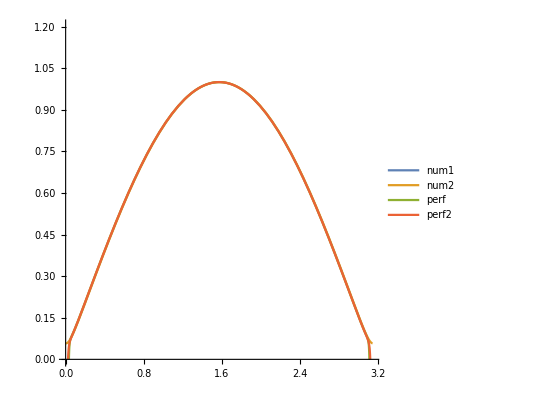

```mathematica
p1=Plot[{u[ϕ]/.sol0[[1]],u[ϕ]/.sol[[1]],perfFull[ϕ],perf[ϕ]},{ϕ,ϕMin, π-0.001},AspectRatio->1,PlotLegends->{"num1","num2","perf","perf2"},PlotRange->{All,{0,1.2}}]
```

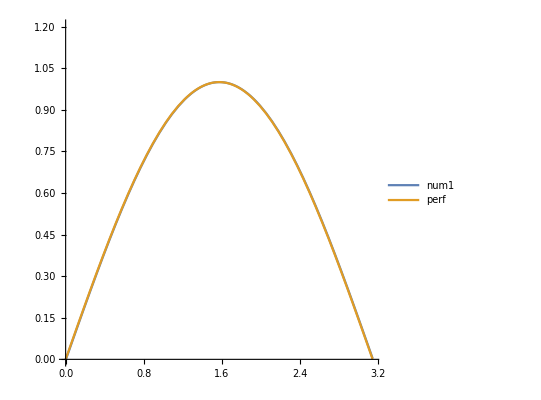

```mathematica
p1=Plot[{u[ϕ]/.sol[[1]],perfFull[ϕ]},{ϕ,ϕMin, π-0.001},AspectRatio->1,PlotLegends->{"num1","perf"},PlotRange->{All,{0,1.2}}]
```